```mathematica
SetDirectory[NotebookDirectory[]];
```

## Uloha 1

### RK4

{{x→Function[{t},ArcTan[16 t]]}}

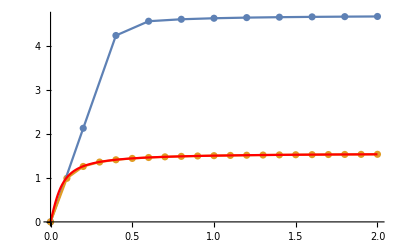

```mathematica
n10 = Import["./outputs/uloha1_RK4_10n.csv","CSV"];
n20 = Import["./outputs/uloha1_RK4_20n.csv","CSV"];
n40 = Import["./outputs/uloha1_RK4_40n.csv","CSV"];
n80 = Import["./outputs/uloha1_RK4_80n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}]
Show[
ListPlot[{n10, n20}],
ListLinePlot[{n10, n20}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### RK2 vs RK4

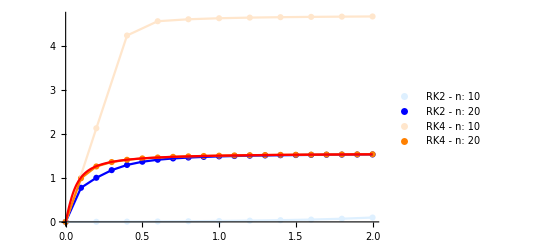

```mathematica
RK220 = Import["./outputs/uloha1_RK2_10n.csv","CSV"];
RK240 = Import["./outputs/uloha1_RK2_20n.csv","CSV"];
RK420 = Import["./outputs/uloha1_RK4_10n.csv","CSV"];
RK440 = Import["./outputs/uloha1_RK4_20n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{RK220, RK240, RK420, RK440}, PlotLegends->{"RK2 - n: 10", "RK2 - n: 20","RK4 - n: 10", "RK4 - n: 20"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
ListLinePlot[{RK220, RK240, RK420, RK440},PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 2

### Taylor tretieho radu

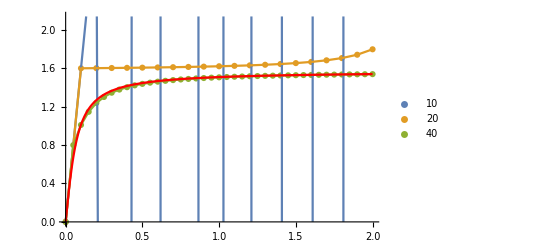

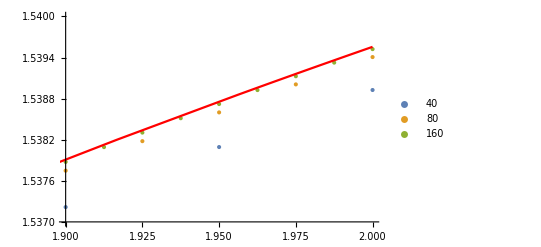

```mathematica
n10 = Import["./outputs/uloha2_tay_10n.csv","CSV"];
n20 = Import["./outputs/uloha2_tay_20n.csv","CSV"];
n40 = Import["./outputs/uloha2_tay_40n.csv","CSV"];
n80 = Import["./outputs/uloha2_tay_80n.csv","CSV"];
n160 = Import["./outputs/uloha2_tay_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"10", "20","40"}],
ListLinePlot[{n10, n20, n40}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n40, n80, n160}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"40", "80", "160"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### Taylor 2 vs Taylor 3

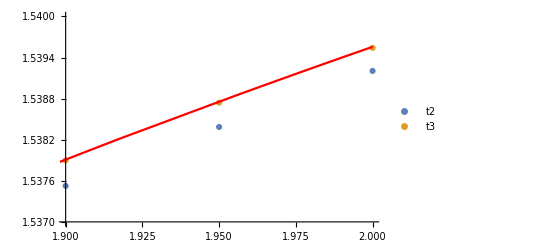

```mathematica
t2 = Import["./outputs/uloha1_tay_40n.csv","CSV"];
t3 = Import["./outputs/uloha2_tay_40n.csv","CSV"];DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{t2, t3}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"t2", "t3"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

## Uloha 3

### RK2

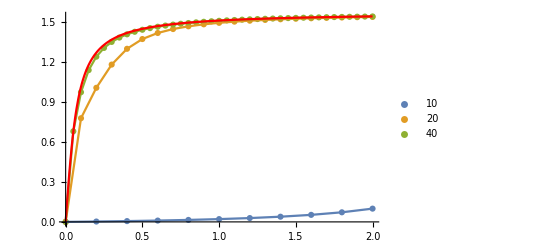

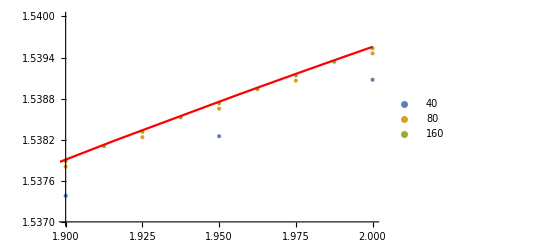

```mathematica
n10 = Import["./outputs/uloha3_RK2_10n.csv","CSV"];
n20 = Import["./outputs/uloha3_RK2_20n.csv","CSV"];
n40 = Import["./outputs/uloha3_RK2_40n.csv","CSV"];
n80 = Import["./outputs/uloha3_RK2_80n.csv","CSV"];
n160 = Import["./outputs/uloha3_RK2_160n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n10, n20, n40}, PlotLegends->{"10", "20","40"}],
ListLinePlot[{n10, n20, n40}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{n40, n80, n160}, PlotRange->{{1.9, 2}, {1.537, 1.54}},PlotLegends->{"40", "80", "160"}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

### RK2 vs Explicit Euler

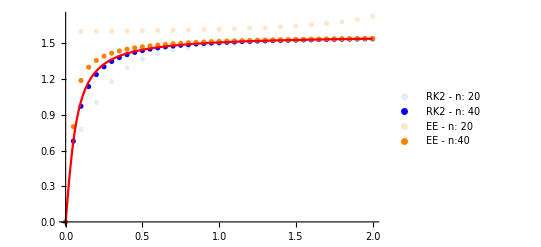

```mathematica
RK220 = Import["./outputs/uloha3_RK2_20n.csv","CSV"];
RK240 = Import["./outputs/uloha3_RK2_40n.csv","CSV"];
EE20 = Import["./outputs/uloha1_eul_20n.csv","CSV"];
EE40 = Import["./outputs/uloha1_eul_40n.csv","CSV"];
DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{RK220, RK240, EE20,EE40}, PlotLegends->{"RK2 - n: 20", "RK2 - n: 40","EE - n: 20", "EE - n:40"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```

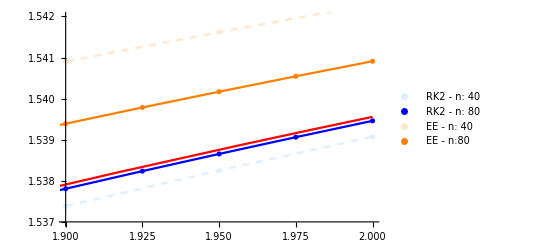

```mathematica
RK240 = Import["./outputs/uloha3_RK2_40n.csv","CSV"];RK280 = Import["./outputs/uloha3_RK2_80n.csv","CSV"];
EE40 = Import["./outputs/uloha1_eul_40n.csv","CSV"];
EE80 = Import["./outputs/uloha1_eul_80n.csv","CSV"];DSolve[{x'[t]==16 Cos[x[t]]^2, x[0]==0},x,{t,0,2}];
Show[
ListPlot[{RK240, RK280, EE40 , EE80}, PlotRange->{{1.9, 2}, {1.537, 1.542}},PlotLegends->{"RK2 - n: 40", "RK2 - n: 80","EE - n: 40", "EE - n:80"}, PlotStyle->{LightBlue, Blue, LightOrange, Orange}],
ListLinePlot[{RK240, RK280, EE40 , EE80}, PlotStyle->{{LightBlue, Dashed}, Blue, {LightOrange, Dashed}, {Orange}}],
Plot[Evaluate[x[t]/.%],{t,0,2}, PlotStyle->Red, PlotRange->All]
]
```